```mathematica
ptMin=0;
ptMax=3;
noPts =5;
width=(ptMax-ptMin)/(noPts-1)//N
```

0.75

```mathematica
xPt=2.22;
idx=IntegerPart[xPt/width]
```

2

```mathematica
secStart=ptMin+idx*width
secEnd=secStart+width
```

1.5

2.25

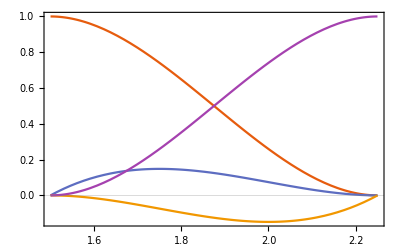

```mathematica
Plot[Evaluate[{1-3 x^2+2 x^3,x-2 x^2+x^3,-(x^2-x^3),3 x^2-2 x^3}/.x->(xVal-secStart)/(secEnd-secStart)],{xVal,secStart,secEnd}]
```

```mathematica
vals=Evaluate[{1-3 x^2+2 x^3,x-2 x^2+x^3,-(x^2-x^3),3 x^2-2 x^3}/.x->(xVal-secStart)/(secEnd-secStart)]/.xVal->xPt
```

{0.004672,0.001536,-0.036864,0.995328}

```mathematica
Total[vals]
```

0.964672